## Prepare

```mathematica
channel=8;
day=3;
dim={channel,day,16,22};
dimH={1, 368, 493};
```

```mathematica
contract[channel_,crop_:{{1,1},{1,1}}]:=NetGraph[{"conv"->{ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[],Ramp,
                                                           ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[],Ramp},
                                   "pooling"->PoolingLayer[{1,2,2},{1,2,2},{0,1,1}],
                                   "cropping"->PartLayer[{;;,crop[[1,1]];;-crop[[1,-1]],crop[[2,1]];;-crop[[2,-1]]}]},
                         {NetPort["Input"]->"conv"->"pooling"->NetPort["Pooling"],"conv"->"cropping"->NetPort["Shortcut"]}]
```

```mathematica
ResizeLayer3D[n_, {dimInx_, dimIny_, dimInz_}] :=
 Block[{sc = 2},
  NetChain[{
    (* Flattens the first two levels so because the next layer only works on 2D arrays *)        
    FlattenLayer[1, "Input" -> {n sc, dimInx, dimIny, dimInz}],    
    (* Doubles the size of the last two dimensions *)        
    ResizeLayer[{Scaled[sc], Scaled[sc]}],
    (* Reshapes the array back to its original order but with the  last two dimensions scaled up from previous layer *)        
    ReshapeLayer[{n sc, dimInx, sc dimIny, sc dimInz}],
    (* Transposes 2nd and 3rd dimensions so that previously unscaled dimension can be actioned *)
    TransposeLayer[2 <-> 3],
    (* Again flatten array a level so that the next later can actually action it *)
    FlattenLayer[1],
    (* Scale only the dimension that hasn't been actioned yet *)        
    ResizeLayer[{Scaled[sc], Scaled[1]}],
    (* Reshape back to original structure but the array now has been scaled up *)
    ReshapeLayer[{n sc, sc dimIny, sc dimInx, sc dimInz}],
    (* importantly, transpose the dimensions back to their original order since it was changed above*)
    TransposeLayer[2 <-> 3],
    (* Now a convolution can be applied to the upsampled up data *)
    ConvolutionLayer[n, 1]}
   ]]
```

```mathematica
ClearAll[expand];
expand[channel_,{dimInx_, dimIny_, dimInz_},pad_:{1,1,1},RAMP_:1]:=NetGraph[
		{"deconv"->{ResizeLayer3D[channel,{dimInx,dimIny,dimInz}],BatchNormalizationLayer[],Ramp,PartLayer[{;;,pad[[1]];;-2,pad[[2]];;-2,pad[[3]];;-2}]},
         "join"->CatenateLayer[],
         "conv"->If[RAMP==1,
                 {ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[],Ramp,
                  ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[],Ramp},
                 {ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[],Ramp,
                  ConvolutionLayer[channel,{3,3,3},"Stride"->1,"PaddingSize"->1],BatchNormalizationLayer[]}]},
        {NetPort["Input"]->"deconv"->"join",NetPort["Shortcut"]->"join"->"conv"}]
```

```mathematica
Unet=NetGraph[<|
  "contract_1"->contract[16],
  "contract_2"->contract[32],
  "contract_3"->contract[64],
  "contract_4"->contract[128],
  "ubase"->{ConvolutionLayer[128,{3,3,3},PaddingSize->1],Ramp,ConvolutionLayer[128,{3,3,3},PaddingSize->1],Ramp,DropoutLayer[0.5]},
  "expand_4"->expand[64,{3,2,3},{3,1,2}],
  "expand_3"->expand[32,{3,3,4},{3,1,1}],
  "expand_2"->expand[16,{3,5,7},{3,1,2}],
  "expand_1"->expand[8,{3,9,12},{3,2,2}]|>,
  {NetPort["Input"]->"contract_1",
   NetPort["contract_1","Pooling"]->"contract_2",
   NetPort["contract_2","Pooling"]->"contract_3",
   NetPort["contract_3","Pooling"]->"contract_4",
   NetPort["contract_4","Pooling"]->"ubase",
   "ubase"->NetPort["expand_4","Input"],
   NetPort["contract_4","Shortcut"]->NetPort["expand_4","Shortcut"],
   NetPort["expand_4","Output"]->NetPort["expand_3","Input"],
   NetPort["contract_3","Shortcut"]->NetPort["expand_3","Shortcut"],
   NetPort["expand_3","Output"]->NetPort["expand_2","Input"],
   NetPort["contract_2","Shortcut"]->NetPort["expand_2","Shortcut"],
    NetPort["expand_2","Output"]->NetPort["expand_1","Input"],
   NetPort["contract_1","Shortcut"]->NetPort["expand_1","Shortcut"]}]
```

NetGraph[<>]

```mathematica
ele=NetChain[{ConvolutionLayer[8,{7,7}],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],
		  ConvolutionLayer[8,{7,7}],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],
		  ConvolutionLayer[8,{7,7}],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],
		  ConvolutionLayer[8,{7,7}],BatchNormalizationLayer[],Ramp,PoolingLayer[2,2],
		  ConvolutionLayer[2,{2,4}],BatchNormalizationLayer[],
		  ReplicateLayer[3],TransposeLayer[]},
 "Input"->dimH];
```

## Regularization

```mathematica
pR=Block[{c=8},
NetGraph[<|"ele"->ele,
           "part"->PartLayer[1;;6],
           "cat"->CatenateLayer[],
           "u"->Unet,
           "simu"->{ConvolutionLayer[1,{1,1,1}],BatchNormalizationLayer[],Ramp,FlattenLayer[1]},
           "thread"->ThreadingLayer[Times],
           "obser"->PartLayer[c],
           "mpart"->PartLayer[c],
           "mse"->MeanSquaredLossLayer[]|>,
    {NetPort["Elevation"]->"ele"->"cat",
     NetPort["Input"]->"part"->"cat"->"u"->"simu"->"thread",
     NetPort["Mask"]->"mpart"->"thread"->"mse",
     NetPort["Input"]->"obser"->"mse"},
   "Elevation"->dimH,
   "Input"->dim,
   "Mask"->dim]];
```

```mathematica
tR=Block[{c=7},
NetGraph[<|"ele"->ele,
           "part"->PartLayer[1;;6],
           "cat"->CatenateLayer[],
           "u"->Unet,
           "simu"->{ConvolutionLayer[1,{1,1,1}],BatchNormalizationLayer[],FlattenLayer[1]},
           "thread"->ThreadingLayer[Times],
           "obser"->PartLayer[c],
           "mpart"->PartLayer[c],
           "mse"->MeanSquaredLossLayer[]|>,
    {NetPort["Elevation"]->"ele"->"cat",
     NetPort["Input"]->"part"->"cat"->"u"->"simu"->"thread",
     NetPort["Mask"]->"mpart"->"thread"->"mse",
     NetPort["Input"]->"obser"->"mse"},
   "Elevation"->dimH,
   "Input"->dim,
   "Mask"->dim]];
```

```mathematica
tomorrowR=NetGraph[<|"ele"->ele,
           "part"->{PartLayer[{All,1;;2}],ConvolutionLayer[6,{2,1,1},"PaddingSize"->{1,0,0}]},
           "cat"->CatenateLayer[],
           "u"->Unet,
           "simu"->{NetMapOperator[ConvolutionLayer[1,{1,1}]],BatchNormalizationLayer[],FlattenLayer[1]},
           "thread"->ThreadingLayer[Times],
           "mpart"->PartLayer[{All,3}],
           "obser"->PartLayer[{All,3}],
           "mse"->MeanSquaredLossLayer[]|>,
    {NetPort["Elevation"]->"ele"->"cat",
     NetPort["Input"]->"part"->"cat"->"u"->"simu"->"thread",
     NetPort["Mask"]->"mpart"->"thread"->"mse",
     NetPort["Input"]->"obser"->"mse"},
   "Elevation"->dimH,
   "Input"->dim,
   "Mask"->dim];
```

```mathematica
yesterdayR=NetGraph[<|"ele"->ele,
           "part"->{PartLayer[{All,2;;3}],ConvolutionLayer[6,{2,1,1},"PaddingSize"->{1,0,0}]},
           "cat"->CatenateLayer[],
           "u"->Unet,
           "simu"->{NetMapOperator[ConvolutionLayer[1,{1,1}]],BatchNormalizationLayer[],FlattenLayer[1]},
           "thread"->ThreadingLayer[Times],
           "mpart"->PartLayer[{All,1}],
           "obser"->PartLayer[{All,1}],
           "mse"->MeanSquaredLossLayer[]|>,
    {NetPort["Elevation"]->"ele"->"cat",
     NetPort["Input"]->"part"->"cat"->"u"->"simu"->"thread",
     NetPort["Mask"]->"mpart"->"thread"->"mse",
     NetPort["Input"]->"obser"->"mse"},
   "Elevation"->dimH,
   "Input"->dim,
   "Mask"->dim];
```

```mathematica
S2O=NetGraph[Flatten[Prepend[{"u"->Unet,"ele"->ele,"blend"->CatenateLayer[],"cate"->CatenateLayer[],"thread"->ThreadingLayer[Times]},
Table[{"part"<>ToString[i]->PartLayer[i;;i],"cat"<>ToString[i]->CatenateLayer[],
	   "post"<>ToString[i]->If[i≠8,{ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[1,{3,3,3},"PaddingSize"->{1,1,1}], BatchNormalizationLayer[]},
			                {ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[1,{3,3,3},"PaddingSize"->{1,1,1}], BatchNormalizationLayer[],Ramp}]},{i,8}]]],		 
Flatten[Append[{NetPort["GCM"]->"blend",NetPort["DEM"]->"ele"->"blend"->"u","cate"->"thread",NetPort["Mask"]->"thread"->NetPort["Obser"]},
Table[{"u"->"cat"<>ToString[i],NetPort["GCM"]->"part"<>ToString[i]->"cat"<>ToString[i]->"post"<>ToString[i]->"cate"},{i,8}]]],
 "GCM"->dim,
 "DEM"->dimH,
 "Mask"->dim];
 
O2S=NetGraph[Flatten[Prepend[{"u"->Unet,"ele"->ele,"blend"->CatenateLayer[],"cate"->CatenateLayer[],"thread"->ThreadingLayer[Times]},
Table[{"part"<>ToString[i]->PartLayer[i;;i],"cat"<>ToString[i]->CatenateLayer[],
	   "post"<>ToString[i]->If[i≠8,{ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[1,{3,3,3},"PaddingSize"->{1,1,1}], BatchNormalizationLayer[]},
			                {ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[32,{3,3,3},"PaddingSize"->{1,1,1}],BatchNormalizationLayer[],Ramp,
			                ConvolutionLayer[1,{3,3,3},"PaddingSize"->{1,1,1}], BatchNormalizationLayer[],Ramp}]},{i,8}]]],		 
Flatten[Append[{NetPort["Obser"]->"blend",NetPort["DEM"]->"ele"->"blend"->"u","cate"->"thread",NetPort["Mask"]->"thread"->NetPort["GCM"]},
Table[{"u"->"cat"<>ToString[i],NetPort["Obser"]->"part"<>ToString[i]->"cat"<>ToString[i]->"post"<>ToString[i]->"cate"},{i,8}]]],
 "Obser"->dim,
 "DEM"->dimH,
 "Mask"->dim];
```

```mathematica
dis=NetChain[{ConvolutionLayer[16,{3,3,3}],
			   BatchNormalizationLayer[],
			   Ramp,
			   FlattenLayer[1],
			   ConvolutionLayer[16,{3,3},"Stride"->2],
			   BatchNormalizationLayer[],
			   Ramp,
			   ConvolutionLayer[16,{3,3}],
			   BatchNormalizationLayer[],
			   Ramp,
			   ConvolutionLayer[16,{3,3}],
			   BatchNormalizationLayer[],
			   FlattenLayer[],
			   1,
			   ElementwiseLayer["HardSigmoid"]
			   },
	"Input"->dim];
DS2O=NetGraph[<|"dis"->{NetMapOperator[dis],FlattenLayer[],ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0]},
				"fake"->PartLayer[1],
				"real"->PartLayer[2]|>,
	{NetPort["Input"]->"dis"->"fake"->NetPort["Fake_S2O"],"dis"->"real"->NetPort["Real_S2O"]},
	"Input"->Prepend[dim,2]];
DO2S=NetGraph[<|"dis"->{NetMapOperator[dis],FlattenLayer[],ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0]},
				"fake"->PartLayer[1],
				"real"->PartLayer[2]|>,
	{NetPort["Input"]->"dis"->"fake"->NetPort["Fake_O2S"],"dis"->"real"->NetPort["Real_O2S"]},
	"Input"->Prepend[dim,2]]
```

NetGraph[<>]

```mathematica
(*2 8 3 16 22*)
ldis=NetChain[{ConvolutionLayer[16,{3,3}],
			   BatchNormalizationLayer[],
			   Ramp,
			   ConvolutionLayer[16,{3,3},"Stride"->2],
			   BatchNormalizationLayer[],
			   Ramp,
			   ConvolutionLayer[16,{3,3}],
			   BatchNormalizationLayer[],
			   Ramp,
			   ConvolutionLayer[16,{3,3}],
			   BatchNormalizationLayer[],
			   FlattenLayer[],
			   1,
			   ElementwiseLayer["HardSigmoid"]
			   },
	"Input"->dim[[2;;]]];
Dvar[var_,dir_]:=NetGraph[<|"part"->PartLayer[{;;,var}],
				       "dis"->{NetMapOperator[ldis],FlattenLayer[],ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0]},
				       "fake"->PartLayer[1],
				       "real"->PartLayer[2]|>,
	{NetPort["Input"]->"part"->"dis",
	"dis"->"fake"->NetPort["Fake_"<>dir<>"_"<>vars[[var]]],
	"dis"->"real"->NetPort["Real_"<>dir<>"_"<>vars[[var]]]},
	"Input"->Prepend[dim,2]]
```

```mathematica
Dvar[1,"S2O"]
```

NetGraph[<>]

```mathematica
S2Of = NetInsertSharedArrays[S2O, "S2O/"];
S2Ob = NetInsertSharedArrays[S2O, "S2O/"];
S2Os = NetInsertSharedArrays[S2O, "S2O/"];

O2Sf = NetInsertSharedArrays[O2S, "O2S/"];
O2Sb = NetInsertSharedArrays[O2S, "O2S/"];
O2Ss = NetInsertSharedArrays[O2S, "O2S/"];
```

```mathematica
pRS=pR;
pRO=pR;
tRS=tR;
tRO=tR;
yesterdayRS=yesterdayR;
yesterdayRO=yesterdayR;
tomorrowRS=tomorrowR;
tomorrowRO=tomorrowR;

pRSmse=1;
pROmse=1;
tRSmse=1;
tROmse=1;
yesterdayRSmse=1;
yesterdayROmse=1;
tomorrowRSmse=1;
tomorrowROmse=1;
```

```mathematica
vars
```

{prmsl,q925,q850,q500,z1000,z850,t2m,p}

## RADA

```mathematica
RADA=NetInitialize[NetGraph[<|
		   "S2Of"->S2Of,
		   "O2Sf"->O2Sf,
		   
		   "Cat_S2O"->CatenateLayer[],
           "Reshape_S2O" -> ReshapeLayer[Prepend[dim,2]],
           "DS2O" -> DS2O,
           
           "Cat_O2S"->CatenateLayer[],
           "Reshape_O2S" -> ReshapeLayer[Prepend[dim,2]],
           "DO2S"->DO2S,
		   
		   "O2Sb"->O2Sb,
		   "S2Ob"->S2Ob,
		   "MSE_S2O2S"->MeanAbsoluteLossLayer[],
		   "MSE_O2S2O"->MeanAbsoluteLossLayer[],
		  
		   "pR_S"->{pRS,ElementwiseLayer[Max[#,pRSmse]-pRSmse &]},
		   "pR_O"->{pRO,ElementwiseLayer[Max[#,pRSmse]-pRSmse &]},
		   "tR_S"->{tRS,ElementwiseLayer[Max[#,tRSmse]-tRSmse &]},
		   "tR_O"->{tRO,ElementwiseLayer[Max[#,tROmse]-tROmse &]},
		   "yesterdayR_S"->{yesterdayRS,ElementwiseLayer[Max[#,yesterdayRSmse]-yesterdayRSmse &]},
		   "yesterdayR_O"->{yesterdayRO,ElementwiseLayer[Max[#,yesterdayROmse]-yesterdayROmse &]},
		   "tomorrowR_S"->{tomorrowRS,ElementwiseLayer[Max[#,tomorrowRSmse]-tomorrowRSmse &]},
		   "tomorrowR_O"->{tomorrowRO,ElementwiseLayer[Max[#,tomorrowROmse]-tomorrowROmse &]},
		
		   
		   "S2Os"->S2Os,
		   "O2Ss"->O2Ss,
		   "MSE_S2Os"->MeanAbsoluteLossLayer[],
		   "MSE_O2Ss"->MeanAbsoluteLossLayer[],
		   
		   (*{"prmsl","q925","q850","q500","z1000","z850","t2m","p"}*)
		   "DS2Oprmsl"->Dvar[1,"S2O"],
		   "DO2Sprmsl"->Dvar[1,"O2S"],
		   
		   "DS2Oq925"->Dvar[2,"S2O"],
		   "DO2Sq925"->Dvar[2,"O2S"],
		   
		   "DS2Oz1000"->Dvar[5,"S2O"],
		   "DO2Sz1000"->Dvar[5,"O2S"],
		   
		   "DS2Ot2m"->Dvar[7,"S2O"],
		   "DO2St2m"->Dvar[7,"O2S"],
		   
		   "DS2Op"->Dvar[8,"S2O"],
		   "DO2Sp"->Dvar[8,"O2S"]
		   |>,
 {NetPort["S"]->NetPort["S2Of","GCM"],
  NetPort["Elevation"]->NetPort["S2Of","DEM"],
  NetPort["Mask"]->NetPort["S2Of","Mask"],
  "S2Of"->"Cat_S2O",
  NetPort["O"]->"Cat_S2O",
  "Cat_S2O"->"Reshape_S2O"->"DS2O",
  
  NetPort["O"]->NetPort["O2Sf","Obser"],
  NetPort["Mask"]->NetPort["O2Sf","Mask"],
  NetPort["Elevation"]->NetPort["O2Sf","DEM"],
  "O2Sf"->"Cat_O2S",
  NetPort["S"]->"Cat_O2S",
  "Cat_O2S"->"Reshape_O2S"->"DO2S",
  
  "S2Of"->NetPort["O2Sb","Obser"],
  NetPort["Mask"]->NetPort["O2Sb","Mask"],
  NetPort["Elevation"]->NetPort["O2Sb","DEM"],
  "O2Sb"->"MSE_S2O2S",
  NetPort["S"]->"MSE_S2O2S"->NetPort["Cycle_S2O"],
  
  "O2Sf"->NetPort["S2Ob","GCM"],
  NetPort["Mask"]->NetPort["S2Ob","Mask"],
  NetPort["Elevation"]->NetPort["S2Ob","DEM"],
  "S2Ob"->"MSE_O2S2O",
  NetPort["O"]->"MSE_O2S2O"->NetPort["Cycle_O2S"],
  
  
  
  "S2Of"->NetPort["pR_O","Input"],
  NetPort["Mask"]->NetPort["pR_O","Mask"],
  NetPort["Elevation"]->NetPort["pR_O","Elevation"],
  "pR_O"->NetPort["Loss_pR_O"],
  
  "S2Of"->NetPort["tR_O","Input"],
  NetPort["Mask"]->NetPort["tR_O","Mask"],
  NetPort["Elevation"]->NetPort["tR_O","Elevation"],
  "tR_O"->NetPort["Loss_tR_O"],
  
  "S2Of"->NetPort["yesterdayR_O","Input"],
  NetPort["Mask"]->NetPort["yesterdayR_O","Mask"],
  NetPort["Elevation"]->NetPort["yesterdayR_O","Elevation"],
  "yesterdayR_O"->NetPort["Loss_yesterdayR_O"],
  
  "S2Of"->NetPort["tomorrowR_O","Input"],
  NetPort["Mask"]->NetPort["tomorrowR_O","Mask"],
  NetPort["Elevation"]->NetPort["tomorrowR_O","Elevation"],
  "tomorrowR_O"->NetPort["Loss_tomorrowR_O"],
  
  "O2Sf"->NetPort["pR_S","Input"],
  NetPort["Mask"]->NetPort["pR_S","Mask"],
  NetPort["Elevation"]->NetPort["pR_S","Elevation"],
  "pR_S"->NetPort["Loss_pR_S"],
  
  "O2Sf"->NetPort["tR_S","Input"],
  NetPort["Mask"]->NetPort["tR_S","Mask"],
  NetPort["Elevation"]->NetPort["tR_S","Elevation"],
  "tR_S"->NetPort["Loss_tR_S"],
  
  "O2Sf"->NetPort["yesterdayR_S","Input"],
  NetPort["Mask"]->NetPort["yesterdayR_S","Mask"],
  NetPort["Elevation"]->NetPort["yesterdayR_S","Elevation"],
  "yesterdayR_S"->NetPort["Loss_yesterdayR_S"],
  
  "O2Sf"->NetPort["tomorrowR_S","Input"],
  NetPort["Mask"]->NetPort["tomorrowR_S","Mask"],
  NetPort["Elevation"]->NetPort["tomorrowR_S","Elevation"],
  "tomorrowR_S"->NetPort["Loss_tomorrowR_S"],
  
  NetPort["O"]->NetPort["S2Os","GCM"],
  NetPort["Mask"]->NetPort["S2Os","Mask"],
  NetPort["Elevation"]->NetPort["S2Os","DEM"],
  "S2Os"->"MSE_S2Os",
  NetPort["O"]->"MSE_S2Os"->NetPort["Loss_Self_S2O"],
 
  NetPort["S"]->NetPort["O2Ss","Obser"],
  NetPort["Mask"]->NetPort["O2Ss","Mask"],
  NetPort["Elevation"]->NetPort["O2Ss","DEM"],
  "O2Ss"->"MSE_O2Ss",
  NetPort["S"]->"MSE_O2Ss"->NetPort["Loss_Self_O2S"],
  
  "Reshape_S2O"->"DS2Oprmsl",
  "Reshape_O2S"->"DO2Sprmsl",
  
  "Reshape_S2O"->"DS2Oq925",
  "Reshape_O2S"->"DO2Sq925",
  
  "Reshape_S2O"->"DS2Oz1000",
  "Reshape_O2S"->"DO2Sz1000",
  
  "Reshape_S2O"->"DS2Ot2m",
  "Reshape_O2S"->"DO2St2m",
  
  "Reshape_S2O"->"DS2Op",
  "Reshape_O2S"->"DO2Sp"
  }]]
```

```mathematica
RADA
```

```mathematica
Length[{"Fake_S2O"->Scaled[s1],"Real_S2O"->Scaled[s1],"Cycle_S2O"->Scaled[-s2],
                  "Fake_O2S"->Scaled[s1],"Real_O2S"->Scaled[s1],"Cycle_O2S"->Scaled[-s2],
                  "Fake_S2O_prmsl"->Scaled[s1],"Real_S2O_prmsl"->Scaled[s1],
                  "Fake_S2O_p"->Scaled[s1],"Real_S2O_p"->Scaled[s1],
                  "Fake_S2O_t2m"->Scaled[s1],"Real_S2O_t2m"->Scaled[s1],
                  "Fake_S2O_q925"->Scaled[s1],"Real_S2O_q925"->Scaled[s1],
                  "Fake_S2O_z1000"->Scaled[s1],"Real_S2O_z1000"->Scaled[s1],
                  "Fake_O2S_prmsl"->Scaled[s1],"Real_O2S_prmsl"->Scaled[s1],
                  "Fake_O2S_p"->Scaled[s1],"Real_O2S_p"->Scaled[s1],
                  "Fake_O2S_t2m"->Scaled[s1],"Real_O2S_t2m"->Scaled[s1],
                  "Fake_O2S_q925"->Scaled[s1],"Real_O2S_q925"->Scaled[s1],
                  "Fake_O2S_z1000"->Scaled[s1],"Real_O2S_z1000"->Scaled[s1],
                  "Loss_Self_S2O"->Scaled[-s3],"Loss_Self_O2S"->Scaled[-s3],
                  "Loss_pR_O"->Scaled[-s4],"Loss_pR_S"->Scaled[-s4],
                  "Loss_tR_O"->Scaled[-s4],"Loss_tR_S"->Scaled[-s4],
                  "Loss_yesterdayR_O"->Scaled[-s4],"Loss_yesterdayR_S"->Scaled[-s4],
                  "Loss_tomorrowR_O"->Scaled[-s4],"Loss_tomorrowR_S"->Scaled[-s4]}]
```

36

## Baselines

#### RADA

```mathematica
RADA=NetInitialize[NetGraph[<|
		   "S2Of"->S2Of,
		   "O2Sf"->O2Sf,
		   "DS2O"->NetMapOperator[DS2O],
		   "DO2S"->NetMapOperator[DO2S],
		   
		   "Cat_S2O"->CatenateLayer[],
           "Reshape_S2O" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_S2O" -> ReshapeLayer[{2}],
           "Fake_S2O"->PartLayer[1],
           "Real_S2O"->PartLayer[2],
           "Scale_S2O" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
           
           "Cat_O2S"->CatenateLayer[],
           "Reshape_O2S" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_O2S" -> ReshapeLayer[{2}],
           "Fake_O2S"->PartLayer[1],
           "Real_O2S"->PartLayer[2],
           "Scale_O2S" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
		   
		   "O2Sb"->O2Sb,
		   "S2Ob"->S2Ob,
		   "MSE_S2O2S"->MeanAbsoluteLossLayer[],
		   "MSE_O2S2O"->MeanAbsoluteLossLayer[](*,
		   
		   "S_pR"->pR, 
		   "O_pR"->pR*)
		   |>,
 {NetPort["S"]->NetPort["S2Of","GCM"],
  NetPort["Elevation"]->NetPort["S2Of","DEM"],
  NetPort["Mask"]->NetPort["S2Of","Mask"],
  "S2Of"->"Cat_S2O",
  NetPort["O"]->"Cat_S2O",
  "Cat_S2O"->"Reshape_S2O"->"DS2O"->"Flat_S2O"->"Scale_S2O",
  "Scale_S2O"->"Fake_S2O"->NetPort["Fake_S2O"],
  "Scale_S2O"->"Real_S2O"->NetPort["Real_S2O"],
  
  NetPort["O"]->NetPort["O2Sf","Obser"],
  NetPort["Mask"]->NetPort["O2Sf","Mask"],
  NetPort["Elevation"]->NetPort["O2Sf","DEM"],
  "O2Sf"->"Cat_O2S",
  NetPort["S"]->"Cat_O2S",
  "Cat_O2S"->"Reshape_O2S"->"DO2S"->"Flat_O2S"->"Scale_O2S",
  "Scale_O2S"->"Fake_O2S"->NetPort["Fake_O2S"],
  "Scale_O2S"->"Real_O2S"->NetPort["Real_O2S"],
  
  "S2Of"->NetPort["O2Sb","Obser"],
  NetPort["Mask"]->NetPort["O2Sb","Mask"],
  NetPort["Elevation"]->NetPort["O2Sb","DEM"],
  "O2Sb"->"MSE_S2O2S",
  NetPort["S"]->"MSE_S2O2S"->NetPort["Cycle_S2O"],
  
  "O2Sf"->NetPort["S2Ob","GCM"],
  NetPort["Mask"]->NetPort["S2Ob","Mask"],
  NetPort["Elevation"]->NetPort["S2Ob","DEM"],
  "S2Ob"->"MSE_O2S2O",
  NetPort["O"]->"MSE_O2S2O"->NetPort["Cycle_O2S"]
  }]]
```

NetGraph[<>]

```mathematica
NetTake[RADA,"S2Of"]
```

NetGraph[<>]

#### Cycle+Dynamic

```mathematica
RADA=NetInitialize[NetGraph[<|
		   "S2Of"->S2Of,
		   "O2Sf"->O2Sf,
		   "DS2O"->NetMapOperator[DS2O],
		   "DO2S"->NetMapOperator[DO2S],
		   
		   "Cat_S2O"->CatenateLayer[],
           "Reshape_S2O" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_S2O" -> ReshapeLayer[{2}],
           "Fake_S2O"->PartLayer[1],
           "Real_S2O"->PartLayer[2],
           "Scale_S2O" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
           
           "Cat_O2S"->CatenateLayer[],
           "Reshape_O2S" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_O2S" -> ReshapeLayer[{2}],
           "Fake_O2S"->PartLayer[1],
           "Real_O2S"->PartLayer[2],
           "Scale_O2S" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
		   
		   "O2Sb"->O2Sb,
		   "S2Ob"->S2Ob,
		   "MSE_S2O2S"->MeanAbsoluteLossLayer[],
		   "MSE_O2S2O"->MeanAbsoluteLossLayer[],
		   
		   "S_pR"->pR, 
		   "O_pR"->pR
		   |>,
 {NetPort["S"]->NetPort["S2Of","GCM"],
  NetPort["Elevation"]->NetPort["S2Of","DEM"],
  NetPort["Mask"]->NetPort["S2Of","Mask"],
  "S2Of"->"Cat_S2O",
  NetPort["O"]->"Cat_S2O",
  "Cat_S2O"->"Reshape_S2O"->"DS2O"->"Flat_S2O"->"Scale_S2O",
  "Scale_S2O"->"Fake_S2O"->NetPort["Fake_S2O"],
  "Scale_S2O"->"Real_S2O"->NetPort["Real_S2O"],
  
  NetPort["O"]->NetPort["O2Sf","Obser"],
  NetPort["Mask"]->NetPort["O2Sf","Mask"],
  NetPort["Elevation"]->NetPort["O2Sf","DEM"],
  "O2Sf"->"Cat_O2S",
  NetPort["S"]->"Cat_O2S",
  "Cat_O2S"->"Reshape_O2S"->"DO2S"->"Flat_O2S"->"Scale_O2S",
  "Scale_O2S"->"Fake_O2S"->NetPort["Fake_O2S"],
  "Scale_O2S"->"Real_O2S"->NetPort["Real_O2S"],
  
  "S2Of"->NetPort["O2Sb","Obser"],
  NetPort["Mask"]->NetPort["O2Sb","Mask"],
  NetPort["Elevation"]->NetPort["O2Sb","DEM"],
  "O2Sb"->"MSE_S2O2S",
  NetPort["S"]->"MSE_S2O2S"->NetPort["Cycle_S2O"],
  
  "O2Sf"->NetPort["S2Ob","GCM"],
  NetPort["Mask"]->NetPort["S2Ob","Mask"],
  NetPort["Elevation"]->NetPort["S2Ob","DEM"],
  "S2Ob"->"MSE_O2S2O",
  NetPort["O"]->"MSE_O2S2O"->NetPort["Cycle_O2S"],
  
  "S2Of"->NetPort["O_pR","Input"],
  NetPort["Elevation"]->NetPort["O_pR","Elevation"],
  NetPort["Mask"]->NetPort["O_pR","Mask"],
  
  "O2Sf"->NetPort["S_pR","Input"],
  NetPort["Elevation"]->NetPort["S_pR","Elevation"],
  NetPort["Mask"]->NetPort["S_pR","Mask"]
  }]]
```

#### Cycle+Self Mapping

```mathematica
S2Of = NetInsertSharedArrays[S2O, "S2O/"];
S2Ob = NetInsertSharedArrays[S2O, "S2O/"];
S2Os = NetInsertSharedArrays[S2O, "S2O/"];

O2Sf = NetInsertSharedArrays[O2S, "O2S/"];
O2Sb = NetInsertSharedArrays[O2S, "O2S/"];
O2Ss = NetInsertSharedArrays[O2S, "O2S/"];
```

```mathematica
RADA=NetInitialize[NetGraph[<|
		   "S2Of"->S2Of,
		   "O2Sf"->O2Sf,
		   "DS2O"->NetMapOperator[DS2O],
		   "DO2S"->NetMapOperator[DO2S],
		   
		   "Cat_S2O"->CatenateLayer[],
           "Reshape_S2O" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_S2O" -> ReshapeLayer[{2}],
           "Fake_S2O"->PartLayer[1],
           "Real_S2O"->PartLayer[2],
           "Scale_S2O" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
           
           "Cat_O2S"->CatenateLayer[],
           "Reshape_O2S" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_O2S" -> ReshapeLayer[{2}],
           "Fake_O2S"->PartLayer[1],
           "Real_O2S"->PartLayer[2],
           "Scale_O2S" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
		   
		   "O2Sb"->O2Sb,
		   "S2Ob"->S2Ob,
		   "MSE_S2O2S"->MeanAbsoluteLossLayer[],
		   "MSE_O2S2O"->MeanAbsoluteLossLayer[],
		   
		   "S2Os"->S2Os,
		   "O2Ss"->O2Ss,
		   "MSE_S2Os"->MeanAbsoluteLossLayer[],
		   "MSE_O2Ss"->MeanAbsoluteLossLayer[]
		   |>,
 {NetPort["S"]->NetPort["S2Of","GCM"],
  NetPort["Elevation"]->NetPort["S2Of","DEM"],
  NetPort["Mask"]->NetPort["S2Of","Mask"],
  "S2Of"->"Cat_S2O",
  NetPort["O"]->"Cat_S2O",
  "Cat_S2O"->"Reshape_S2O"->"DS2O"->"Flat_S2O"->"Scale_S2O",
  "Scale_S2O"->"Fake_S2O"->NetPort["Fake_S2O"],
  "Scale_S2O"->"Real_S2O"->NetPort["Real_S2O"],
  
  NetPort["O"]->NetPort["O2Sf","Obser"],
  NetPort["Mask"]->NetPort["O2Sf","Mask"],
  NetPort["Elevation"]->NetPort["O2Sf","DEM"],
  "O2Sf"->"Cat_O2S",
  NetPort["S"]->"Cat_O2S",
  "Cat_O2S"->"Reshape_O2S"->"DO2S"->"Flat_O2S"->"Scale_O2S",
  "Scale_O2S"->"Fake_O2S"->NetPort["Fake_O2S"],
  "Scale_O2S"->"Real_O2S"->NetPort["Real_O2S"],
  
  "S2Of"->NetPort["O2Sb","Obser"],
  NetPort["Mask"]->NetPort["O2Sb","Mask"],
  NetPort["Elevation"]->NetPort["O2Sb","DEM"],
  "O2Sb"->"MSE_S2O2S",
  NetPort["S"]->"MSE_S2O2S"->NetPort["Cycle_S2O"],
  
  "O2Sf"->NetPort["S2Ob","GCM"],
  NetPort["Mask"]->NetPort["S2Ob","Mask"],
  NetPort["Elevation"]->NetPort["S2Ob","DEM"],
  "S2Ob"->"MSE_O2S2O",
  NetPort["O"]->"MSE_O2S2O"->NetPort["Cycle_O2S"],
  
  NetPort["O"]->NetPort["S2Os","GCM"],
  NetPort["Elevation"]->NetPort["S2Os","DEM"],
  NetPort["Mask"]->NetPort["S2Os","Mask"],
  "S2Os"->"MSE_S2Os",
  NetPort["O"]->"MSE_S2Os"->NetPort["S2O_Self"],
  
  NetPort["S"]->NetPort["O2Ss","Obser"],
  NetPort["Elevation"]->NetPort["O2Ss","DEM"],
  NetPort["Mask"]->NetPort["O2Ss","Mask"],
  "O2Ss"->"MSE_O2Ss",
  NetPort["S"]->"MSE_O2Ss"->NetPort["O2S_Self"]
  }]]
```

NetGraph[<>]

```mathematica
(*NetTrain[cycleGAN,
    {Function[Block[{base,choice,choice2},
        base=RandomSample[Range[2,length],#BatchSize];
        choice=Map[Block[{daylag=RandomSample[Range[-15,15]][[1]],yearlag=RandomSample[Range[-5,5]][[1]],tempt},
                                tempt=#+daylag+yearlag*365;
                                If[And[tempt>0,tempt<=length],tempt,#]]&,base];
        <|"P_GCM"->nP4GCM[[base]],
          "D_GCM"->ndynamics4GCM[[base]],
          "P_Obser"->nP4Obser[[choice]],
          "D_Obser"->ndynamics4Obser[[choice]]|>]], "RoundLength" -> Length[nP4GCM]},
    LossFunction ->{"FakeLoss_GCM->Obser"->Scaled[1],"RealLoss_GCM->Obser"->Scaled[1],"ReconstructionLoss_GCM->Obser"->Scaled[-hype[[3]]],
                    "FakeLoss_Obser->GCM"->Scaled[1],"RealLoss_Obser->GCM"->Scaled[1],"ReconstructionLoss_Obser->GCM"->Scaled[-hype[[3]]],
                    "Loss_Obser2GCM_SelfRegression"->Scaled[-hype[[3]]],"Loss_GCM2Obser_SelfRegression"->Scaled[-hype[[3]]],
                    "Loss_RDownscaling_GCM"->Scaled[-hype[[3]]],"Loss_RDownscaling_Obser"->Scaled[-hype[[3]]]},
    TrainingUpdateSchedule -> {"Discriminator_GCM->Obser"|"Discriminator_Obser->GCM",
                               "Generator_GCM->Obser"|"Generator_Obser->GCM",
                               "Cycle_GCM->Obser"|"Cycle_Obser->GCM",
                               "Generator_GCM->Obser_SelfRegression"|"Generator_Obser->GCM_SelfRegression"},
    LearningRateMultipliers -> {"Scale_GCM->Obser" -> 0, "Scale_Obser->GCM" -> 0,
                             "Generator_GCM->Obser" -> -1,"Generator_Obser->GCM"->-1,
                             "Generator_GCM->Obser_SelfRegression" -> -1,"Generator_Obser->GCM_SelfRegression"->-1,
                             "Cycle_GCM->Obser"->-1,"Cycle_Obser->GCM"->-1,
                             "Discriminator_Obser->GCM"->1,"Discriminator_GCM->Obser"->1,
                             "R_Downscaling_GCM"->0,"R_Downscaling_Obser"->0},
    BatchSize -> 32,
    TargetDevice->"GPU",
    MaxTrainingRounds->400,
    Method -> {"ADAM", "Beta1" -> 0.5, "LearningRate" -> 10^-4,
                           "WeightClipping" -> {"Discriminator_Obser->GCM"-> hype[[2]]/100.,"Discriminator_GCM->Obser"->hype[[2]]/100.}},
    TrainingProgressReporting -> {{Function@ReportCycleGan2[#Net], "Interval" -> Quantity[300, "Batches"]},"Print"}]*)
```

```mathematica
pRS=pR;
pRO=pR;
tRS=tR;
tRO=tR;
yesterdayRS=yesterdayR;
yesterdayRO=yesterdayR;
tomorrowRS=tomorrowR;
tomorrowRO=tomorrowR;
```

```mathematica
pR
```

NetGraph[<>]

```mathematica
RADA=NetInitialize[NetGraph[<|
		   "S2Of"->S2Of,
		   "O2Sf"->O2Sf,
		   "DS2O"->NetMapOperator[DS2O],
		   "DO2S"->NetMapOperator[DO2S],
		   
		   "Cat_S2O"->CatenateLayer[],
           "Reshape_S2O" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_S2O" -> ReshapeLayer[{2}],
           "Fake_S2O"->PartLayer[1],
           "Real_S2O"->PartLayer[2],
           "Scale_S2O" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
           
           "Cat_O2S"->CatenateLayer[],
           "Reshape_O2S" -> ReshapeLayer[Prepend[dim,2]],
           "Flat_O2S" -> ReshapeLayer[{2}],
           "Fake_O2S"->PartLayer[1],
           "Real_O2S"->PartLayer[2],
           "Scale_O2S" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
		   
		   "O2Sb"->O2Sb,
		   "S2Ob"->S2Ob,
		   "MSE_S2O2S"->MeanAbsoluteLossLayer[],
		   "MSE_O2S2O"->MeanAbsoluteLossLayer[],
		  
		   "pR_S"->pRS,
		   "pR_O"->pRO,
		   "tR_S"->tRS,
		   "tR_O"->tRO,
		   "yesterdayR_S"->yesterdayRS,
		   "yesterdayR_O"->yesterdayRO,
		   "tomorrowR_S"->tomorrowRS,
		   "tomorrowR_O"->tomorrowRO
		   |>,
 {NetPort["S"]->NetPort["S2Of","GCM"],
  NetPort["Elevation"]->NetPort["S2Of","DEM"],
  NetPort["Mask"]->NetPort["S2Of","Mask"],
  "S2Of"->"Cat_S2O",
  NetPort["O"]->"Cat_S2O",
  "Cat_S2O"->"Reshape_S2O"->"DS2O"->"Flat_S2O"->"Scale_S2O",
  "Scale_S2O"->"Fake_S2O"->NetPort["Fake_S2O"],
  "Scale_S2O"->"Real_S2O"->NetPort["Real_S2O"],
  
  NetPort["O"]->NetPort["O2Sf","Obser"],
  NetPort["Mask"]->NetPort["O2Sf","Mask"],
  NetPort["Elevation"]->NetPort["O2Sf","DEM"],
  "O2Sf"->"Cat_O2S",
  NetPort["S"]->"Cat_O2S",
  "Cat_O2S"->"Reshape_O2S"->"DO2S"->"Flat_O2S"->"Scale_O2S",
  "Scale_O2S"->"Fake_O2S"->NetPort["Fake_O2S"],
  "Scale_O2S"->"Real_O2S"->NetPort["Real_O2S"],
  
  "S2Of"->NetPort["O2Sb","Obser"],
  NetPort["Mask"]->NetPort["O2Sb","Mask"],
  NetPort["Elevation"]->NetPort["O2Sb","DEM"],
  "O2Sb"->"MSE_S2O2S",
  NetPort["S"]->"MSE_S2O2S"->NetPort["Cycle_S2O"],
  
  "O2Sf"->NetPort["S2Ob","GCM"],
  NetPort["Mask"]->NetPort["S2Ob","Mask"],
  NetPort["Elevation"]->NetPort["S2Ob","DEM"],
  "S2Ob"->"MSE_O2S2O",
  NetPort["O"]->"MSE_O2S2O"->NetPort["Cycle_O2S"],
  
  
  
  "S2Of"->NetPort["pR_O","Input"],
  NetPort["Mask"]->NetPort["pR_O","Mask"],
  NetPort["Elevation"]->NetPort["pR_O","Elevation"],
  "pR_O"->NetPort["Loss_pR_O"],
  
  "S2Of"->NetPort["tR_O","Input"],
  NetPort["Mask"]->NetPort["tR_O","Mask"],
  NetPort["Elevation"]->NetPort["tR_O","Elevation"],
  "tR_O"->NetPort["Loss_tR_O"],
  
  "S2Of"->NetPort["yesterdayR_O","Input"],
  NetPort["Mask"]->NetPort["yesterdayR_O","Mask"],
  NetPort["Elevation"]->NetPort["yesterdayR_O","Elevation"],
  "yesterdayR_O"->NetPort["Loss_yesterdayR_O"],
  
  "S2Of"->NetPort["tomorrowR_O","Input"],
  NetPort["Mask"]->NetPort["tomorrowR_O","Mask"],
  NetPort["Elevation"]->NetPort["tomorrowR_O","Elevation"],
  "tomorrowR_O"->NetPort["Loss_tomorrowR_O"],
  
  "O2Sf"->NetPort["pR_S","Input"],
  NetPort["Mask"]->NetPort["pR_S","Mask"],
  NetPort["Elevation"]->NetPort["pR_S","Elevation"],
  "pR_S"->NetPort["Loss_pR_S"],
  
  "O2Sf"->NetPort["tR_S","Input"],
  NetPort["Mask"]->NetPort["tR_S","Mask"],
  NetPort["Elevation"]->NetPort["tR_S","Elevation"],
   "tR_S"->NetPort["Loss_tR_S"],
  
  "O2Sf"->NetPort["yesterdayR_S","Input"],
  NetPort["Mask"]->NetPort["yesterdayR_S","Mask"],
  NetPort["Elevation"]->NetPort["yesterdayR_S","Elevation"],
  "yesterdayR_S"->NetPort["Loss_yesterdayR_S"],
  
  "O2Sf"->NetPort["tomorrowR_S","Input"],
  NetPort["Mask"]->NetPort["tomorrowR_S","Mask"],
  NetPort["Elevation"]->NetPort["tomorrowR_S","Elevation"],
  "tomorrowR_S"->NetPort["Loss_tomorrowR_S"]
  }]]
```

NetGraph[<>]

```mathematica
vars={"prmsl", "q925", "q850", "q500", "z1000", "z850", "t2m","p"};
```

```mathematica
{correction,obser,raw}=Import["/Users/pan11/tempt.mx"];
```

```mathematica
Dimensions[correction]
Dimensions[obser]
Dimensions[raw]
```

{400,8,3,16,22}

{400,8,3,16,22}

{400,8,3,16,22}

```mathematica
day=RandomSample[Range[400]][[1]]
TableForm[Table[Map[MatrixPlot[#[[day,var,2]],PlotLegends->Automatic]&,{correction,obser,raw}],{var,8}],TableHeadings->{vars,{"Corr","Obser","Raw"}},TableAlignments->Center]
```

79

| Corr | Obser | Raw
prmsl | -Graphics- | -Graphics- | -Graphics-
q925 | -Graphics- | -Graphics- | -Graphics-
q850 | -Graphics- | -Graphics- | -Graphics-
q500 | -Graphics- | -Graphics- | -Graphics-
z1000 | -Graphics- | -Graphics- | -Graphics-
z850 | -Graphics- | -Graphics- | -Graphics-
t2m | -Graphics- | -Graphics- | -Graphics-
p | -Graphics- | -Graphics- | -Graphics-

```mathematica
pp=RandomSample[Range[Length[obser]]][[1;;400]];
TableForm[Table[Map[MatrixPlot[Mean[#[[pp,var,2]]],PlotLegends->Automatic]&,{correction,obser,raw}],{var,8}],TableHeadings->{vars,{"Corr","Obser","Raw"}},TableAlignments->Center]
```

| Corr | Obser | Raw
prmsl | -Graphics- | -Graphics- | -Graphics-
q925 | -Graphics- | -Graphics- | -Graphics-
q850 | -Graphics- | -Graphics- | -Graphics-
q500 | -Graphics- | -Graphics- | -Graphics-
z1000 | -Graphics- | -Graphics- | -Graphics-
z850 | -Graphics- | -Graphics- | -Graphics-
t2m | -Graphics- | -Graphics- | -Graphics-
p | -Graphics- | -Graphics- | -Graphics-

```mathematica
var=-2;
Correlation[Flatten[Mean[correction[[;;,var,2]]]],Flatten[Mean[raw[[;;,var,2]]]]]
Correlation[Flatten[Mean[obser[[;;,var,2]]]],Flatten[Mean[raw[[;;,var,2]]]]]
Correlation[Flatten[Mean[correction[[;;,var,2]]]],Flatten[Mean[obser[[;;,var,2]]]]]
```

0.572799

-0.0529168

-0.34501

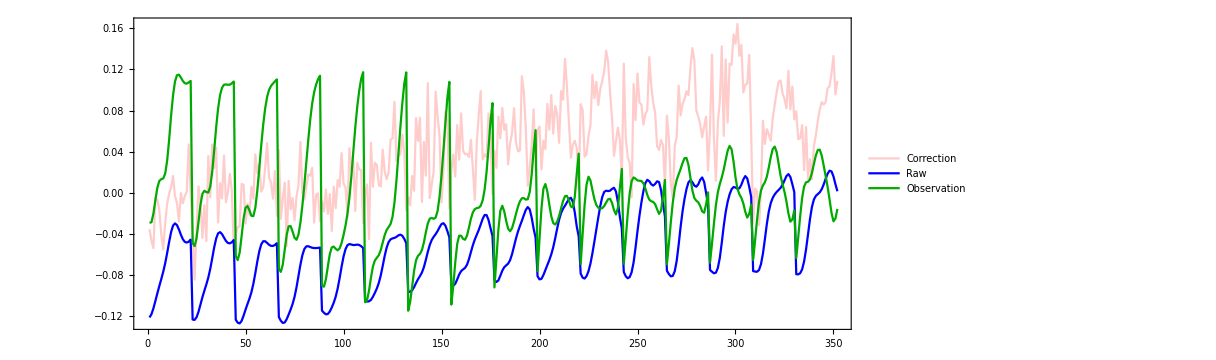
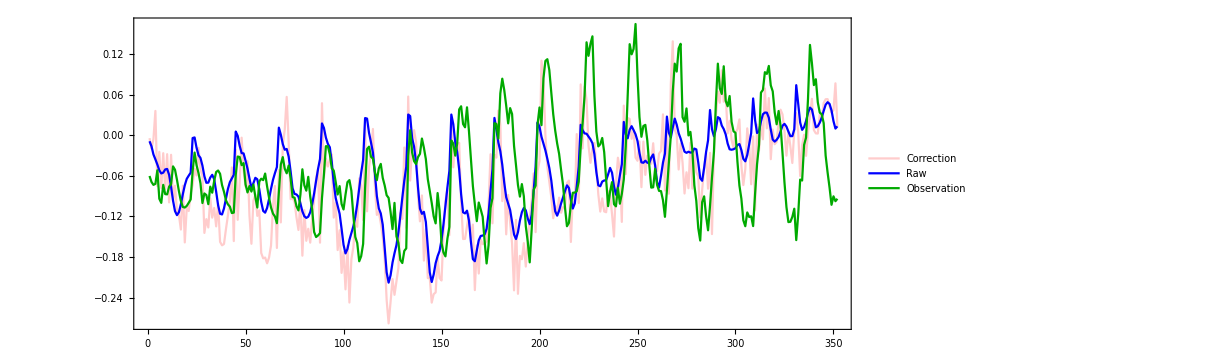
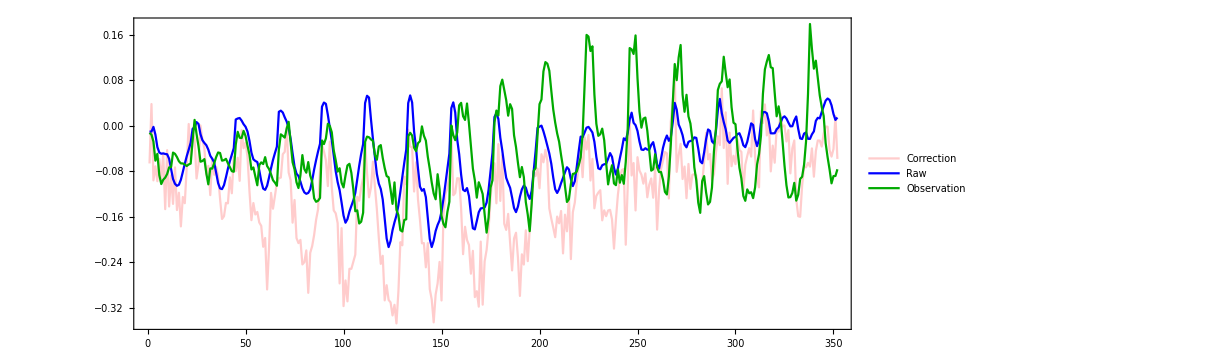
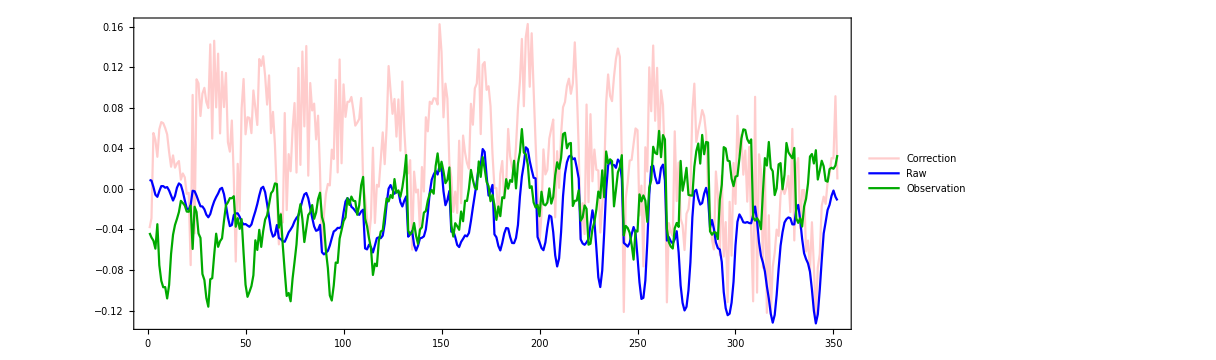
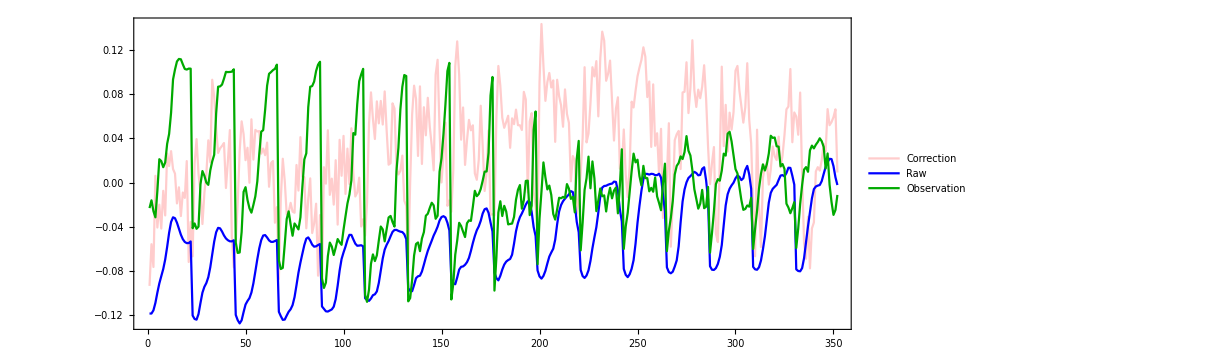
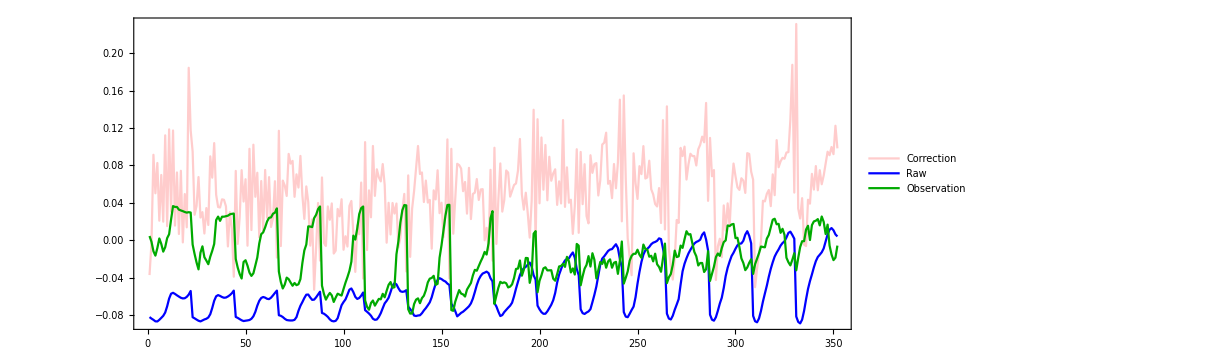
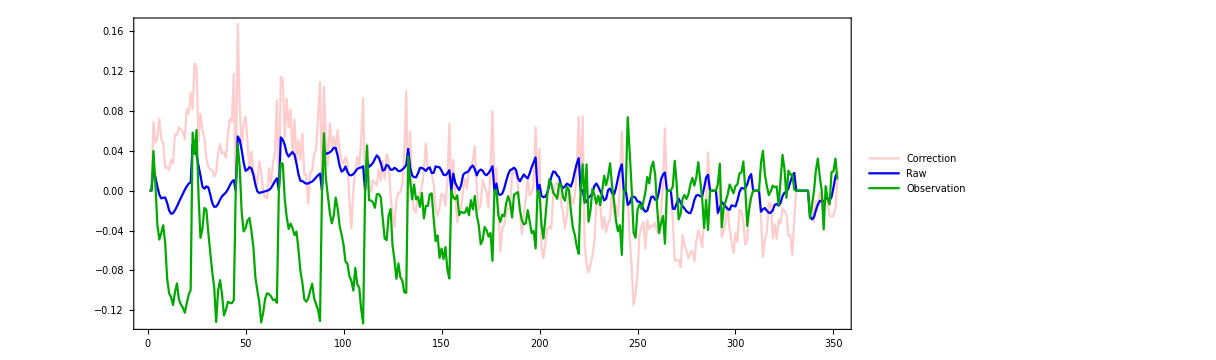
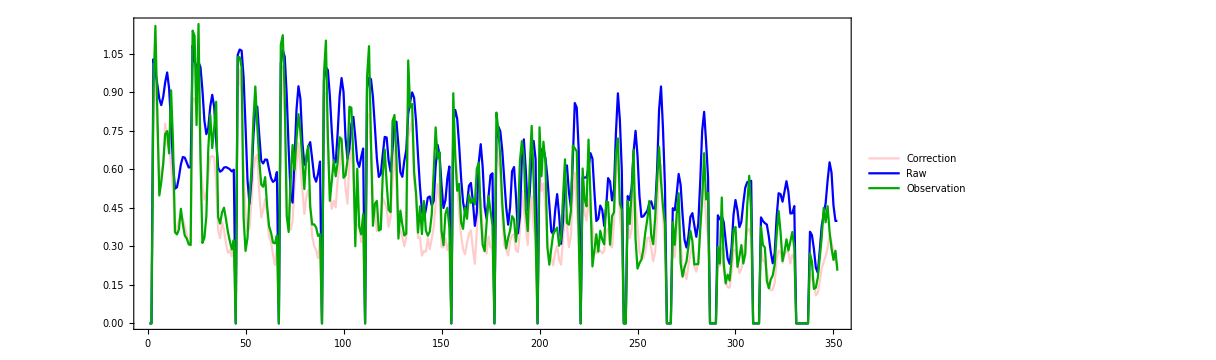

```mathematica
Table[ListLinePlot[{Flatten[Mean[correction[[;;,var,2]]]],Flatten[Mean[raw[[;;,var,2]]]],Flatten[Mean[obser[[;;,var,2]]]]},PlotStyle->{{Red,Opacity[.2]},Blue,Darker[Green]},ImageSize->900,AspectRatio->.4,Frame->True,
PlotLegends->Placed[{"Correction","Raw","Observation"},Right]],{var,8}]
```

```mathematica
index="q"
"/usr/workspace/pan11/CycleGAN_HD/Result/RADA_"<>index<>"_"<>StringRiffle[Map[ToString,{s1,s2,s3,s4,s5}],"_"]<>".mx"
```

q

/usr/workspace/pan11/CycleGAN_HD/Result/RADA_q_1_2_4_8_16.mx

```mathematica
{s1,s2,s3,s4,s5}=Table[RandomSample[{1,2,4,8,16,32}][[1]],{5}]
```

{8,2,2,32,2}

```mathematica
DatePlus[{2010,4,1},-280]
```

{2009,6,25}

```mathematica
MinMax[correction]
MinMax[raw]
MinMax[obser]
```

{-8.15264,6.72604}

{-7.24518,6.40022}

{-5.03096,6.19061}

```mathematica
day=RandomSample[position][[1]];
MatrixPlot[correction[[day,-1,2]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
MatrixPlot[raw[[day,-1,2]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
MatrixPlot[obser[[day,-1,2]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*{correction,obser,raw}=Map[Normal[#][[1;;308]]&,{correction,obser,raw}];*)
{correction,obser,raw}=Map[Normal,{correction,obser,raw}];
```

```mathematica
mask=Import["/Users/pan11/mask.mx"]
ele=NumericArray[{Log[Import["/Users/pan11/Elevation.mx"][[1]]+1.]},"Real32"]
model=Import["/Users/pan11/b.mx"]
```

NumericArray[…]

NumericArray[…]

NetGraph[<>]

```mathematica
x1=raw[[309]];
x2=raw[[313]];
(*y=model[<|"S"->x,"Mask"->mask,"Elevation"->ele|>];*)
```

```mathematica
(*Set[x1[[1,;;,10;;16,15;;22]],x1[[1,;;,10;;16,15;;22]]-RandomReal[{0.05,.06},{3,7,8}]];*)
```

```mathematica
Dimensions[x1[[1,;;,10;;16,15;;22]]]
```

{3,7,8}

```mathematica
y11=model[<|"S"->x1,"Mask"->mask,"Elevation"->ele|>];
y2=model[<|"S"->x2,"Mask"->mask,"Elevation"->ele|>];
MinMax[Normal[y1]]
MinMax[Normal[y2]]
```

{-317.028,477.653}

{-2.67994,3.35395}

```mathematica
model
```

NetGraph[<>]

```mathematica
Dimensions[Join[RandomReal[{0,2},{7,3,16,22}],RandomReal[{0,2},{1,3,16,22}]]]
```

{8,3,16,22}

```mathematica
Table[Block[{tempt,y},
y=mm[<|"GCM"->Join[RandomReal[{-2,2},{7,3,16,22}],RandomReal[{0,2},{1,3,16,22}]],"DEM"->ele|>];
tempt=MinMax[Normal[y]];
Print[tempt];
tempt],{i,100}]
```

{-1.4383,1.15663}

{-1.95849,1.88906}

{-0.549845,0.778725}

{-4.21173,1.34106}

{-3.00737,1.57386}

{-2.7345,0.918376}

{-2.4557,1.65611}

{-2.02052,1.13792}

{-1.99011,1.0723}

{-3.83612,1.71816}

{-2.50604,1.54317}

{-2.05038,1.62763}

{-1.44512,0.38922}

{-2.2857,1.60257}

{-2.92132,1.13723}

{-2.03793,0.957592}

{-1.60675,1.76298}

{-2.35973,1.40305}

{-2.09302,0.902227}

{-1.96433,1.79053}

{-1.80804,1.15218}

{-2.04888,1.41776}

{-2.95107,1.47157}

{-11.2106,17.3339}

{-1.7406,1.19991}

{-2.19598,1.64328}

{-1.71958,1.11552}

{-1.72193,0.780371}

{-2.61314,1.31042}

{-2.40356,1.60949}

{-2.25865,0.736034}

{-2.00029,1.35388}

{-1.29048,2.01316}

{-1.49453,0.75707}

{-3.53157,1.42257}

{-2.04352,1.33456}

{-778.305,1120.18}

{-1.84045,1.07084}

{-1.83301,0.996204}

{-2.1608,1.44013}

$Aborted

```mathematica
Unet=NetExtract[mm,"u"]
```

NetGraph[<>]

```mathematica
mm=Import["/Users/pan11/bb.mx"]
```

NetGraph[<>]

```mathematica
y12=mm[<|"GCM"->x1,"DEM"->ele|>]
```

NumericArray[…]

```mathematica
z=Normal[y11-y12];
```

```mathematica
MinMax[Normal[y1]]
```

{-317.028,477.653}

```mathematica
MinMax[z]
MinMax[x1]
```

{-2.96188,317.028}

{-2.96188,2.87108}

```mathematica
MinMax[Normal[y1]]
```

{-317.028,477.653}

```mathematica
,
```

```mathematica
vars
```

{prmsl,q925,q850,q500,z1000,z850,t2m,p}

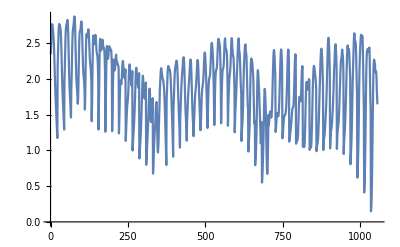
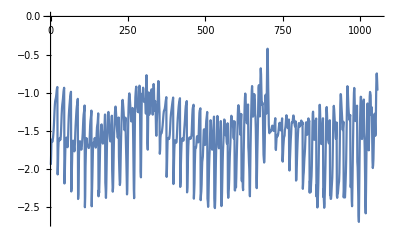
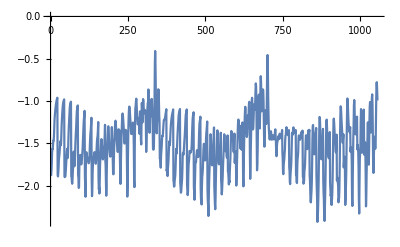
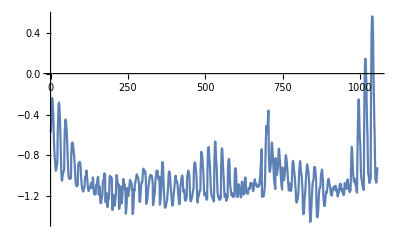
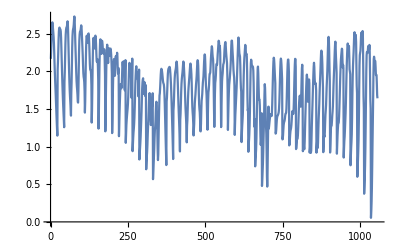
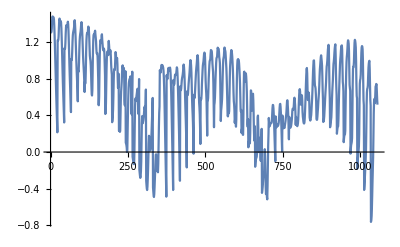
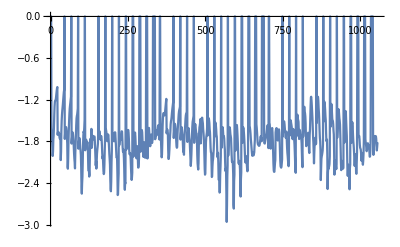
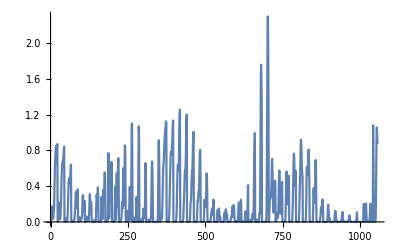

```mathematica
Map[ListLinePlot[Flatten[#],PlotRange->Full]&,x1]
Map[ListLinePlot[Flatten[#],PlotRange->Full]&,x2]
```

```mathematica
MatrixPlot[y1[[1,1]],PlotLegends->Automatic,PlotRange->{-5,5}]
MatrixPlot[x1[[1,1]],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

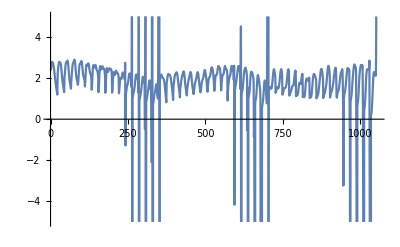
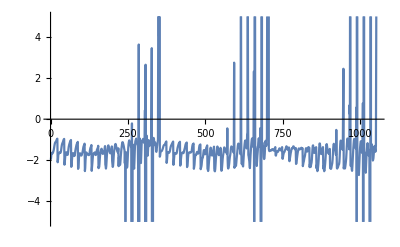
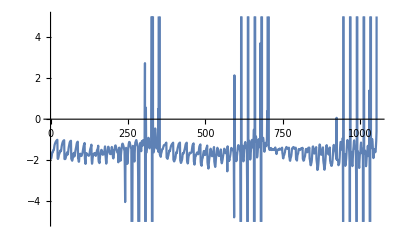
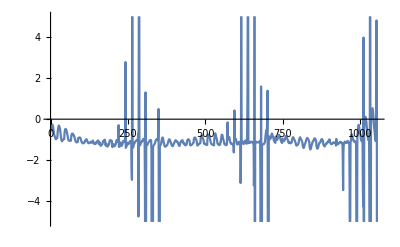
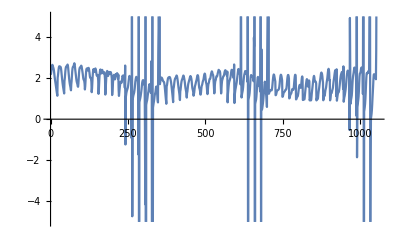
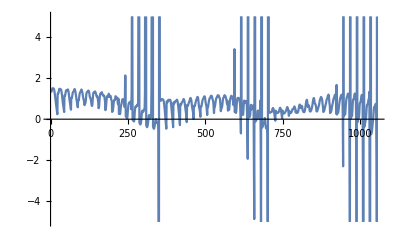
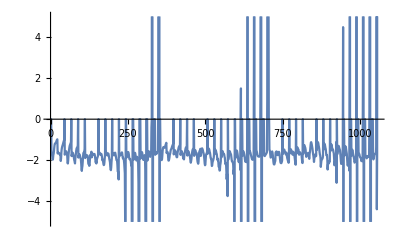
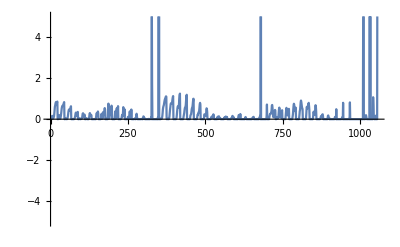

```mathematica
Map[ListLinePlot[Flatten[#],PlotRange->{-5,5}]&,Normal[y1]]
Map[ListLinePlot[Flatten[#],PlotRange->Full]&,Normal[y2]]
```

```mathematica
TableForm[Map[Map[MatrixPlot[#,PlotLegends->Automatic,PlotRange->Full]&,#]&,Normal[x]]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
DO2S=NetInitialize[NetChain[{ConvolutionLayer[16,{3,3,3}],
                           BatchNormalizationLayer[],
                           Ramp,
                           FlattenLayer[1],
                           ConvolutionLayer[16,{3,3},"Stride"->2],
                           BatchNormalizationLayer[],
                           Ramp,
                           ConvolutionLayer[16,{3,3}],
                           BatchNormalizationLayer[],
                           Ramp,
                           ConvolutionLayer[16,{3,3}],
                           BatchNormalizationLayer[],
                           FlattenLayer[],
                           2,
                           SoftmaxLayer[]
                           },
        "Input"->dim,
        "Output"->NetDecoder[{"Class",{-1,1}}]]]
```

NetChain[<>]

```mathematica
DO2S[RandomReal[{-1,1},{8,3,16,22}]]
```

{0.494048,0.505952}

```mathematica
MinMax[Normal[y]]
```

{-1.3794,3.67537}

```mathematica
position=Position[correction,_?(Abs[#]>30&)];
DeleteDuplicates[position[[;;,1]]]
```

{309,314,329,378,389,528}

```mathematica
DeleteDuplicates[position[[;;,1]]]
```

{309,314,329,378,389,528}

```mathematica
Information[model]
```

Net Information

NetGraph[<>]

```mathematica
model[<|"S"->
```

```mathematica
day1=1;
day2=2;
```

```mathematica
Position[Map[Max[#[[7]]]&,obser],0.][[;;,1]]
```

{13,14,17,24,31,32,35,36,43,53,60,63,64,67,68,76,77,86,93,95,98,100,103,107,110,112,118,119,124,131,134,135,136,138,139,141,142,144,147,154,155,156,160,162,163,167,168,171,172,175,182,211,212,218,231,237,240,246,252,255,259,261,271,276,278,284,291,293,295,300,308,309,312,313,314,317,320,324,325,329,331,333,335,337,338,342,352,356,358,361,369,374,376,378,380,389,402,404,408,413,430,431,445,446,448,456,459,462,470,478,482,492,516,518,521,522,524,526,527,528,529,535,538,539,542,545,553,564,567,568,569,570,571,578,582,585,589,590,595,599}

```mathematica
Map[Max[#[[8]]]&,obser]
```

```mathematica
Map[MinMax,raw[[day1]]]
Map[Map[MinMax,raw[[#]]]&,DeleteDuplicates[position[[;;,1]]]]
```

{{-1.5604,1.25232},{-2.34899,0.856757},{-2.06231,0.726052},{-1.4059,1.37077},{-1.55369,1.26738},{-1.14363,1.2074},{-0.190884,2.06199},{0.,2.04199}}

{{{0.147191,2.87108},{-2.6941,-0.423012},{-2.42961,-0.408204},{-1.44971,0.558862},{0.0540148,2.72859},{-0.76351,1.48146},{-2.96188,0.},{0.,2.29627}},{{0.592942,4.919},{-1.98134,1.04526},{-2.07708,1.1524},{-1.28624,1.3291},{0.617842,4.63599},{0.20566,3.07441},{-2.58269,0.},{0.,2.70016}},{{0.792564,3.7457},{-2.30661,0.620767},{-2.47306,1.49394},{-1.44608,1.61785},{0.769657,3.6807},{0.50426,2.74755},{-1.98053,0.},{0.,3.20107}},{{-1.94322,4.33252},{-2.81954,2.02453},{-2.43414,1.77135},{-1.47442,1.49582},{-2.01132,3.7916},{-2.46094,2.38292},{-4.83429,0.},{0.,3.49282}},{{-0.671356,4.29001},{-2.67042,0.754072},{-2.407,1.07732},{-1.32996,1.61522},{-0.700319,3.7916},{-0.961548,2.38292},{-3.88519,0.},{0.,4.46869}},{{-0.120609,3.20267},{-2.46746,0.907269},{-2.18156,0.994133},{-1.40557,1.52822},{-0.201218,3.11414},{-1.14728,1.80473},{-2.50078,0.},{0.,2.71242}}}

```mathematica
TableForm[{Map[MatrixPlot[#[[1]],PlotLegends->Automatic]&,raw[[day1]]],
Map[MatrixPlot[#[[1]],PlotLegends->Automatic]&,correction[[day1]]],
Map[MatrixPlot[#[[1]],PlotLegends->Automatic]&,raw[[day2]]],
Map[MatrixPlot[#[[1]],PlotLegends->Automatic]&,correction[[day2]]]},
TableHeadings->{None, vars},TableAlignments->Center]
```

prmsl | q925 | q850 | q500 | z1000 | z850 | t2m | p
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
range=Block[{tempt=Range[Length[correction]]},
Map[Set[tempt,DeleteCases[tempt,#]]&,DeleteDuplicates[position[[;;,1]]]];tempt];
{correction,obser,raw}=Map[Normal[#][[range]]&,{correction,obser,raw}];
```

```mathematica
vars={"prmsl", "q925", "q850", "q500", "z1000", "z850", "t2m","p"};
```

```mathematica
MinMax[correction]
MinMax[obser]
MinMax[raw]
```

{-6.24466,7.29886}

{-5.39439,6.19061}

{-6.23935,7.32489}

```mathematica
net[["O2Sf"]]
```

NetGraph[<>]

```mathematica
Dimensions[correction]
```

{308,8,3,16,22}

```mathematica
var=1;
Correlation[Flatten[Mean[Mean[correction[[;;,var,;;]]]]],Flatten[Mean[Mean[raw[[;;,var,;;]]]]]]
Correlation[Flatten[Mean[Mean[obser[[;;,var,;;]]]]],Flatten[Mean[Mean[raw[[;;,var,;;]]]]]]
Correlation[Flatten[Mean[Mean[correction[[;;,var,;;]]]]],Flatten[Mean[Mean[obser[[;;,var,;;]]]]]]
```

0.336607

-0.131663

-0.254215

```mathematica
var=8;
cut=1;
MatrixPlot[Mean[Mean[correction[[;;,var,;;,1;;-cut,1;;-cut]]]],PlotLegends->Automatic]
MatrixPlot[Mean[Mean[raw[[;;,var,;;,1;;-cut,1;;-cut]]]],PlotLegends->Automatic]
MatrixPlot[Mean[Mean[obser[[;;,var,;;,1;;-cut,1;;-cut]]]],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
{MinMax[correction[[day]]],MinMax[raw[[day]]],MinMax[obser[[day]]]}
```

{{-309.442,479.181},{-2.96188,2.87108},{-2.35077,3.71283}}

```mathematica
position=Position[correction,_?(Abs[#]>100&)];
```

```mathematica
DeleteDuplicates[position[[;;,1]]]
```

{309,314,329,378,389,528}

```mathematica
day=309;var=1;
TableForm[Table[{MatrixPlot[correction[[day,var,2]],PlotLegends->Automatic],
MatrixPlot[raw[[day,var,2]],PlotLegends->Automatic],
MatrixPlot[obser[[day,var,2]],PlotLegends->Automatic]},{var,8}],TableHeadings->{vars,{"Correction","Raw","Obser"}},TableAlignments->Center]
```

| Correction | Raw | Obser
prmsl | -Graphics- | -Graphics- | -Graphics-
q925 | -Graphics- | -Graphics- | -Graphics-
q850 | -Graphics- | -Graphics- | -Graphics-
q500 | -Graphics- | -Graphics- | -Graphics-
z1000 | -Graphics- | -Graphics- | -Graphics-
z850 | -Graphics- | -Graphics- | -Graphics-
t2m | -Graphics- | -Graphics- | -Graphics-
p | -Graphics- | -Graphics- | -Graphics-

```mathematica
cut=1;
Table[ListLinePlot[{Flatten[Mean[Mean[correction[[;;,var,;;,1;;-cut,1;;-cut]]]]],Flatten[Mean[Mean[raw[[;;,var,;;,1;;-cut,1;;-cut]]]]],Flatten[Mean[Mean[obser[[;;,var,;;,1;;-cut,1;;-cut]]]]]},
PlotRange->Full,PlotStyle->{Red,Blue,Darker[Green]},ImageSize->700,AspectRatio->.3,PlotRange->Full,
Frame->True,PlotLabel->vars[[var]]],{var,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
net
```

NetGraph[<>]

```mathematica
Table[MinMax[correction[[;;,i]]],{i,8}]
Table[MinMax[raw[[;;,i]]],{i,8}]
```

{{-499.829,532.648},{-261.444,1111.28},{-167.341,897.572},{-860.904,77.1071},{-211.664,1353.61},{-78.3746,639.345},{-733.625,695.475},{0.,106.371}}

{{-6.09782,5.69107},{-2.88495,5.30997},{-2.52042,5.36472},{-1.5399,7.32489},{-6.23935,4.90155},{-6.0609,3.13041},{-4.83429,2.84238},{0.,4.91171}}

```mathematica
Mean[Mean[correction[[;;,var]]]]
```

{{-0.00591585,0.0064695,0.0071035,-0.0178511,-0.0151621,-0.0172968,0.0169834,0.0124149,0.00459172,0.0194608,0.0172868,0.0303911,0.00918992,-0.0211878,-0.0106408,-0.000454811,-0.0178885,-0.00569694,-0.00344562,-0.00350038,-0.00858241,-0.0110367},{-0.0167853,-0.00447259,-0.0198869,-0.0446627,-0.0328844,0.035935,0.0306015,0.00385824,0.00742214,0.0151561,-0.0154415,-0.0402801,-0.0756274,-0.0761731,-0.0914935,-0.0918366,-0.10932,-0.109983,-0.110985,-0.0626822,-0.0449266,-0.0226592},{-0.0299959,-0.00633614,-0.0267585,-0.044941,0.0257059,0.0690792,0.0754375,0.0196798,0.0255495,0.0251485,0.0347643,-0.0265387,-0.0200741,-0.0672435,-0.109793,-0.156233,-0.0937032,-0.115569,-0.113364,-0.10317,-0.0998975,-0.0404861},{-0.07101,-0.0295649,-0.0303044,-0.0213741,0.0280128,0.10788,0.0488749,0.0591242,0.0751651,0.0228925,0.0168497,-0.0100981,-0.0533264,-0.114635,-0.192344,-0.21396,-0.214189,-0.189205,-0.190968,-0.178494,-0.150402,-0.0571771},{-0.130016,-0.0696444,-0.0333181,0.0656329,0.155387,0.170585,0.0872864,0.124808,0.117224,0.0331913,0.00456768,-0.0651085,-0.0786289,-0.105809,-0.186681,-0.255152,-0.225319,-0.212041,-0.19433,-0.156763,-0.13677,-0.0749872},{-0.151331,-0.0563599,0.0968737,0.181654,0.2124,0.145682,0.160459,0.159102,0.130095,0.0654329,-0.0150214,-0.0474773,-0.102213,-0.118481,-0.132662,-0.154057,-0.199351,-0.147582,-0.149682,-0.133007,-0.15599,-0.0693688},{-0.155149,0.0137407,0.110824,0.16308,0.193516,0.185727,0.126863,0.147383,0.161754,0.098495,-0.0189397,-0.100122,-0.178219,-0.201416,-0.243649,-0.22389,-0.199963,-0.140793,-0.141116,-0.0926028,-0.0869352,-0.04118},{-0.13522,-0.0137544,0.0825486,0.105181,0.066265,0.122188,0.148085,0.145476,0.128215,0.0397757,-0.0000229099,-0.143009,-0.169051,-0.225741,-0.214275,-0.251004,-0.232705,-0.214715,-0.14656,-0.0720013,-0.0427254,-0.0130235},{-0.171145,-0.0541208,-0.0463582,0.0114969,0.110772,0.136189,0.156412,0.157185,0.123152,0.0585942,-0.0179688,-0.0893698,-0.160464,-0.270406,-0.290928,-0.270374,-0.299658,-0.22868,-0.173224,-0.0221239,0.0258634,0.00640162},{-0.149818,-0.0940134,-0.00735063,0.0124798,0.11523,0.128348,0.133107,0.112287,0.0733607,0.0555528,0.0379375,-0.0629969,-0.17447,-0.247434,-0.25776,-0.21923,-0.267396,-0.247406,-0.142236,0.00152688,0.0179126,0.0214849},{-0.156494,-0.0741649,-0.0413257,0.0250895,0.00553111,0.0941917,0.0558752,0.0225821,0.101553,0.0284039,-0.056888,-0.0736002,-0.167302,-0.231647,-0.266254,-0.196615,-0.222174,-0.264266,-0.145307,-0.00360242,-0.041358,0.0692271},{-0.122863,-0.0113118,-0.027619,0.00977225,0.0306798,0.0707158,0.0710405,0.0609647,0.0360843,-0.0648575,-0.0835271,-0.0875757,-0.128935,-0.217807,-0.173398,-0.120196,-0.182739,-0.180242,-0.114317,-0.0732312,-0.187464,0.243584},{-0.0513434,0.0195759,-0.0121856,0.0200953,0.0774486,0.101214,0.0295482,0.0618649,-0.0338252,0.00796131,-0.0278993,-0.0159674,-0.0900497,-0.105281,-0.141524,-0.11575,-0.125507,-0.131698,-0.165748,-0.184713,-0.463501,0.753239},{-0.0532819,-0.0210422,0.00909746,0.0654643,0.10295,0.162028,0.0919534,0.132207,0.0773352,0.0341877,0.0194954,0.0335543,-0.0152118,-0.0519854,-0.0611604,0.00544087,-0.0969847,-0.085267,-0.0666964,-0.443766,-0.523261,1.68566},{-0.0440744,-0.0549336,-0.0300184,0.0377227,0.119253,0.14346,0.195304,0.187504,0.155218,0.121735,0.109314,0.0897527,0.0535683,0.0304476,0.0315821,0.0378307,0.0318218,0.14255,0.0147601,-0.534545,-0.0179678,2.60707},{-0.0492828,-0.0531527,-0.0425017,-0.0207332,0.00133385,0.0164896,0.0236772,0.0262361,0.0213637,0.00827542,-0.00661802,-0.0207771,-0.0308719,-0.0357805,-0.0317284,-0.0192756,-0.00569328,-0.00222759,-0.019325,0.510725,2.46324,3.07321}}

```mathematica
var=3;
MatrixPlot[Mean[Mean[correction[[;;,var]]]]]
MatrixPlot[Mean[Mean[obser[[;;,var]]]]]
MatrixPlot[Mean[Mean[raw[[;;,var]]]]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Table[MinMax[raw[[;;,i]]],{i,8}]
```

{{-5.58399,5.48839},{-3.07796,5.54706},{-2.73496,5.70741},{-1.53934,8.1304},{-5.71242,4.93614},{-5.34527,3.21502},{-5.29467,2.89363},{0.,4.70319}}

```mathematica
Table[MinMax[obser[[;;,i]]],{i,8}]
```

{{-5.81756,3.93612},{-2.72794,4.9802},{-2.53919,4.88066},{-1.62865,5.56371},{-6.0323,3.93365},{-5.39439,2.994},{-3.5676,2.80071},{0.,5.00976}}

```mathematica
position=Position[correction,_?(Abs[#]>8&)];
```

```mathematica
position
```

{{6,2,2,13,1},{6,2,2,13,2},{6,2,2,13,3},{6,2,2,14,1},{6,2,2,14,2},{6,2,2,14,3},{6,2,2,15,1},{6,2,2,16,1},{6,2,3,12,2},{6,2,3,12,3},{6,2,3,13,1},{6,2,3,13,2},{6,2,3,13,3},{6,2,3,13,4},{6,2,3,14,1},{6,2,3,14,2},{6,2,3,14,3},{6,2,3,14,4},{6,2,3,15,1},{6,2,3,15,2},{6,2,3,15,3},{6,2,3,16,1},{6,2,3,16,2},{6,3,2,12,3},{6,3,2,12,4},{6,3,2,13,3},2346,{211,8,3,12,5},{211,8,3,12,6},{211,8,3,12,7},{211,8,3,13,4},{211,8,3,13,5},{211,8,3,13,6},{211,8,3,13,7},{211,8,3,13,8},{211,8,3,14,5},{211,8,3,14,6},{211,8,3,14,7},{211,8,3,14,8},{211,8,3,14,9},{211,8,3,15,5},{211,8,3,15,6},{211,8,3,15,7},{211,8,3,15,8},{211,8,3,15,9},{211,8,3,15,10},{211,8,3,15,11},{211,8,3,16,8},{211,8,3,16,9},{211,8,3,16,10},{211,8,3,16,11},{211,8,3,16,12}}
 |  |  |  |

```mathematica
MatrixPlot[raw[[366,8,3]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MinMax[correction[[366,8,3]]]
```

{-0.908635,0.901439}

```mathematica
MatrixPlot[correction[[366,8,3]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[correction[[40,1,1]]]
MatrixPlot[raw[[40,1,1]]]
```

-Graphics-

-Graphics-

```mathematica
position[[1]]
```

{6,2,2,13,1}

```mathematica
Correlation[Flatten[Mean[correction[[;;,var,day]]]],Flatten[Mean[raw[[;;,var,day]]]]]
Correlation[Flatten[Mean[correction[[;;,var,day]]]],Flatten[Mean[obser[[;;,var,day]]]]]
Correlation[Flatten[Mean[obser[[;;,var,day]]]],Flatten[Mean[raw[[;;,var,day]]]]]
```

0.291602

0.270887

0.54757

```mathematica
var=3;
day=1;
TableForm[Table[{MatrixPlot[Mean[correction[[;;,var,day]]],PlotLegends->Automatic],
MatrixPlot[Mean[obser[[;;,var,day]]],PlotLegends->Automatic],
MatrixPlot[Mean[raw[[;;,var,day]]],PlotLegends->Automatic]},{var,8}]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
!
```

```mathematica
correction[[1,1,1]]
```

{{-0.271049,-0.529309,-0.52844,-0.4441,-0.464783,-0.347487,-0.225926,-0.104934,0.000975591,0.058841,0.111771,0.186099,0.248222,0.320349,0.335371,0.383335,0.400615,0.386545,0.517093,0.407619,0.436905,0.303503},{-0.362149,-0.751065,-0.604348,-0.697081,-0.544191,-0.526536,-0.377974,-0.272241,-0.178319,0.00197926,0.125915,0.249206,0.303347,0.347151,0.448899,0.478243,0.489951,0.59911,0.684477,0.687505,0.624554,0.309288},{-0.276095,-0.652887,-0.677367,-0.74004,-0.551346,-0.516939,-0.319536,-0.237844,-0.122676,0.0215167,0.123845,0.201878,0.187941,0.244381,0.328022,0.397489,0.418713,0.542186,0.637898,0.72089,0.703107,0.340452},{-0.171501,-0.736544,-0.690148,-0.705007,-0.45297,-0.495175,-0.372135,-0.236511,-0.12598,-0.0078825,0.0369307,0.023324,0.0626736,0.0592539,0.136582,0.151088,0.29342,0.420227,0.579812,0.616099,0.631176,0.378575},{-0.115608,-0.729099,-0.610582,-0.507105,-0.378404,-0.386011,-0.2596,-0.117509,-0.00295738,0.0500388,0.0508527,0.0799162,0.0876063,0.121699,0.132262,0.167062,0.268124,0.380087,0.502154,0.590108,0.619033,0.468406},{-0.148099,-0.599074,-0.483734,-0.288136,-0.158269,-0.0483301,0.0674925,0.111715,0.185939,0.240839,0.207137,0.198845,0.26284,0.287699,0.283742,0.313507,0.319981,0.373543,0.491241,0.555382,0.62169,0.460484},{-0.109162,-0.426573,-0.317866,-0.135312,0.0656031,0.332041,0.403542,0.392775,0.394569,0.398768,0.376557,0.376504,0.433935,0.461423,0.557922,0.423547,0.46908,0.391646,0.5025,0.613908,0.667831,0.498093},{-0.0124363,-0.230288,-0.226868,-0.0852857,0.160693,0.392218,0.519945,0.474554,0.480599,0.381582,0.413196,0.446579,0.558618,0.707344,0.675281,0.569219,0.574545,0.522287,0.572913,0.733577,0.754434,0.555112},{0.0197882,-0.375479,-0.15618,-0.124729,0.095706,0.193351,0.463691,0.522285,0.493049,0.59195,0.568076,0.66447,0.721572,0.784011,0.787586,0.691839,0.709556,0.628937,0.681923,0.813154,0.710591,0.637564},{0.0994616,-0.233561,-0.151187,-0.199915,-0.206097,-0.032967,0.185005,0.378985,0.544519,0.609455,0.663052,0.710525,0.797454,0.809852,0.800722,0.782451,0.791768,0.666119,0.752677,0.749468,0.688779,0.583448},{0.253307,-0.227036,-0.233556,-0.201771,-0.221769,-0.210769,-0.0144308,0.189831,0.517205,0.674509,0.650626,0.783555,0.731379,0.841012,0.886449,0.825668,0.882591,0.751018,0.801727,0.755716,0.763874,0.500845},{-0.0553889,0.258979,-0.0150908,0.0211687,-0.362344,-0.353799,-0.0433924,0.270224,0.550619,0.689661,0.681145,0.722775,0.808836,0.743791,0.87421,0.850843,0.850268,0.843068,0.800493,0.729858,0.710203,0.466606},{0.203607,0.233444,0.269936,-0.240145,-0.254462,-0.303367,-0.0806714,0.347787,0.546444,0.659393,0.783958,0.753234,0.686775,0.714805,0.810703,0.771188,0.829807,0.748935,0.717229,0.674602,0.655285,0.612511},{0.497669,0.579639,0.529538,0.195954,-0.111575,-0.131854,0.037491,0.32803,0.525459,0.675671,0.678622,0.704826,0.642135,0.699525,0.741259,0.719662,0.799955,0.703439,0.65899,0.63532,0.660666,0.545835},{0.144086,0.0803647,0.0712704,0.279172,-0.0515847,-0.191296,-0.0398892,0.201299,0.56788,0.773277,0.747711,0.683089,0.589115,0.604355,0.699549,0.720997,0.768317,0.725074,0.755091,0.791792,0.766805,0.592785},{0.165976,0.207168,0.287667,0.161595,-0.0446355,-0.0646527,-0.0581335,0.326007,0.493257,0.561736,0.525926,0.457357,0.394457,0.391819,0.438754,0.518173,0.592185,0.623551,0.696894,0.652034,0.563819,0.483475}}

```mathematica
Correlation[Flatten[correction[[1,1,1]]],Flatten[raw[[1,1,1]]]]
```

0.454045

```mathematica
MatrixPlot[correction[[1,1,1]]]
MatrixPlot[obser[[1,1,1]]]
MatrixPlot[raw[[1,1,1]]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
process=ToExpression[Select[Import["/Users/pan11/slurm-1385129.out","Table"],Length[#]==38&][[2;;]]];
```

```mathematica
TableForm[{Range[38],process[[2]]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38
0 | 1 | 3 | 192 | 23 | 6.26×10^-6 | 7 s | 2635 h41m29s | -15. | â.80.94 | -1.5 | â.80.94 | 1.54 | â.80.94 | -1. | â.80.94 | -1.5 | â.80.94 | 1.49 | â.80.94 | -1. | â.80.94 | -1.2 | â.80.94 | -2.2 | â.80.94 | -2.1 | â.80.94 | -2.6 | â.80.94 | -0.95 | â.80.94 | -1.3 | â.80.94 | -1.1 | â.80.94 | -2. | â.80.94

```mathematica
process[[2,-3]]
```

â.80.94

```mathematica
ListLinePlot[process[[;;,-4]],ImageSize->800,AspectRatio->.5]
```

-Graphics-

```mathematica
{correction,obser,raw}=Import["/Users/pan11/tempt.mx"];
```

```mathematica
correction=Mean[Normal[correction]];
{obser,raw}=Normal[{obser,raw}];
```

```mathematica
Dimensions[correction]
Dimensions[obser]
Dimensions[raw]
```

{8,182,16,22}

{8,182,16,22}

{8,182,16,22}

```mathematica
Map[MatrixPlot[Mean[#[[8]]]]&,{correction,obser,raw}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
TableForm[Table[
{Correlation[Flatten[Mean[correction[[var]]]],Flatten[Mean[obser[[var]]]]],
Correlation[Flatten[Mean[raw[[var]]]],Flatten[Mean[obser[[var]]]]]},{var,8}]]
```

0.826504 | 0.970293
0.698483 | 0.606706
0.774525 | 0.711737
0.847174 | 0.925206
0.784339 | 0.956593
0.704629 | 0.893688
0.948542 | 0.96363
0.90135 | 0.837881

## Forecast

```mathematica
result=Import["/Users/pan11/result_aa2d0f68.mx"];
```

```mathematica
position=Position[result[[;;,1]],_?(Head[#]==NumericArray&)][[;;,1]];
```

```mathematica
obser=result[[position,1]];
```

```mathematica
raw=result[[position,2]];
```

```mathematica
correction=result[[position,3]];
```

```mathematica
Dimensions[obser[[1]]]
```

{8,182,16,22}

```mathematica
var=-2;
MatrixPlot[Mean[Flatten[Normal[obser[[;;,var]]],1]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
MatrixPlot[Mean[Flatten[Normal[Table[raw[[i]][[;;,var]],{i,Length[raw]}]],2]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
MatrixPlot[Mean[Flatten[Normal[Table[correction[[i]][[;;,var]],{i,Length[raw]}]],2]],PlotLegends->Automatic,ColorFunction->"Rainbow"]
Correlation[Flatten[Mean[Flatten[Normal[Table[correction[[i]][[;;,var]],{i,Length[raw]}]],2]]],Flatten[Mean[Flatten[Normal[obser[[;;,var]]],1]]]]
Correlation[Flatten[Mean[Flatten[Normal[Table[raw[[i]][[;;,var]],{i,Length[raw]}]],2]]],Flatten[Mean[Flatten[Normal[obser[[;;,var]]],1]]]]
```

-Graphics-

-Graphics-

-Graphics-

0.956553

0.986781

```mathematica
mraw=Map[Map[Mean,#]&,Table[Mean[Normal[raw[[i]]]],{i,Length[raw]}]];
mobser=Map[Map[Mean,#]&,Normal[obser]];
```

```mathematica
mcorrection3=Map[Map[Mean,#]&,Table[Mean[Normal[correction[[i]]]],{i,Length[correction]}]];
```

```mathematica
mcorrection2=Map[Map[Mean,#]&,Table[Mean[Normal[correction[[i]]]],{i,Length[correction]}]];
```

```mathematica
mcorrection1=Map[Map[Mean,#]&,Table[Mean[Normal[correction[[i]]]],{i,Length[correction]}]];
```

```mathematica
mcorrection=(mcorrection1+mcorrection2+mcorrection3)/3.;
```

```mathematica
Dimensions[mraw]
Dimensions[mcorrection]
Dimensions[mobser]
```

{19,8,16,22}

{19,8,16,22}

{19,8,16,22}

```mathematica
TableForm[Table[
{Correlation[Flatten[mobser[[year,-1]]],Flatten[mcorrection[[year,-1]]]],
Correlation[Flatten[mobser[[year,-1]]],Flatten[mraw[[year,-1]]]]},{year,19}]]
```

0.947664 | 0.857854
0.961931 | 0.868789
0.965048 | 0.857223
0.943608 | 0.829854
0.946365 | 0.815814
0.948616 | 0.822605
0.957929 | 0.843254
0.960241 | 0.843103
0.92672 | 0.799574
0.97402 | 0.852918
0.972045 | 0.853657
0.926543 | 0.815195
0.968082 | 0.872188
0.957997 | 0.847684
0.935698 | 0.804894
0.923136 | 0.797721
0.896634 | 0.787954
0.916097 | 0.788493
0.950953 | 0.857002

```mathematica
TableForm[Table[{Correlation[Flatten[Mean[mobser[[;;,var]]]],Flatten[Mean[mcorrection[[;;,var]]]]],
Correlation[Flatten[Mean[mobser[[;;,var]]]],Flatten[Mean[mraw[[;;,var]]]]]},{var,8}]]
```

0.769596 | 0.715216
0.809592 | 0.750409
0.861934 | 0.824041
0.961737 | 0.969982
0.760163 | 0.723319
0.819367 | 0.85045
0.974545 | 0.986706
0.965986 | 0.853534

```mathematica
year=RandomSample[Range[19]][[1]];
day=RandomSample[Range[170]][[1]];
{MatrixPlot[correction[[year,1,-1,day]],ImageSize->400],MatrixPlot[raw[[year,1,-1,day]],ImageSize->400]}
```

{-Graphics-,-Graphics-}

```mathematica
var=8;
corr1=Table[If[Variance[mobser[[;;,var,i,j]]]>0,Correlation[mraw[[;;,var,i,j]],mobser[[;;,var,i,j]]],-1],{i,16},{j,22}];
corr2=Table[If[Variance[mobser[[;;,var,i,j]]]>0,Correlation[mcorrection[[;;,var,i,j]],mobser[[;;,var,i,j]]],-1],{i,16},{j,22}];
```

```mathematica
Mean[Select[Flatten[corr1],Positive]]
Mean[Select[Flatten[corr2],Positive]]
```

0.301294

0.278774

```mathematica
SmoothHistogram[{Select[Flatten[corr1],#>0.&],Select[Flatten[corr2],#>0.&]},PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
MatrixPlot[corr2-corr1,PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[corr1,PlotLegends->Automatic]
MatrixPlot[corr2,PlotLegends->Automatic]
```

```mathematica
-Graphics--Graphics-
```

-Graphics-

```mathematica
var=-1;
{mraw,mobser,mcorrection}=Map[Table[Mean[#[[year,var]]],{year,Length[raw]}]&,{raw,obser,correction}];
```

```mathematica
Mean[Select[Flatten[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mcorrection[[;;,i,j]]],Null],{i,16},{j,22}]],#>-.4&]]
Mean[Select[Flatten[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mraw[[;;,i,j]]],Null],{i,16},{j,22}]],#>-.4&]]
```

0.28452

0.216442

```mathematica
SmoothHistogram[{Select[Flatten[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mcorrection[[;;,i,j]]],Null],{i,16},{j,22}]],#>-.4&],
				Select[Flatten[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mraw[[;;,i,j]]],Null],{i,16},{j,22}]],#>-.4&]},PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
MinMax[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mcorrection[[;;,i,j]]],Null],{i,16},{j,22}]]
MinMax[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mraw[[;;,i,j]]],Null],{i,16},{j,22}]]
```

{Min[-0.0537932,Null],Max[0.648172,Null]}

{Min[-0.265569,Null],Max[0.698246,Null]}

```mathematica
MatrixPlot[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mcorrection[[;;,i,j]]],Null],{i,16},{j,22}],PlotLegends->Automatic]
MatrixPlot[Table[If[Variance[mraw[[;;,i,j]]]>0,Correlation[mobser[[;;,i,j]],mraw[[;;,i,j]]],Null],{i,16},{j,22}],PlotLegends->Automatic]
```

-Graphics-

-Graphics-